# MA-Trader

## Initialization

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
```

```mathematica
indexesDataset = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","DJI_NASDAQ_MXX_NIKKEI_datasetV2.wdx"}]];
ipc = indexesDataset[[3]];
samplePrices = Take[ipc["Prices"],{8000,-1}];
params = FindProcessParameters[samplePrices,OrnsteinUhlenbeckProcess[μ,σ,θ,x0]];
```

```mathematica
GeneratePrices[n_]:=Block[{generated},
generated = RandomFunction[OrnsteinUhlenbeckProcess[μ,σ,θ,x0]/.params,{0,n-1,1}];
First[Normal[generated]]
];
```

## 1-SMA Crossover Strategy

```mathematica
SMA1Strategy[datedPrices_, window_,transactionCost_]:=Block[{ma,prices,paddedDatedPrices,lookingFor,buy={}, sell={}},
ma = MovingAverage[datedPrices[[All,2]],window];
prices  = Drop[datedPrices[[All,2]],window-1];
paddedDatedPrices = Drop[datedPrices,window-1];

lookingFor = If[First[ma]<First[prices],"SellSignal","BuySignal"];

Do[
If[lookingFor == "SellSignal" && ma[[i]]>prices[[i]],
AppendTo[sell,paddedDatedPrices[[i]]];
lookingFor = "BuySignal";
];
If[lookingFor == "BuySignal" && ma[[i]]<prices[[i]],
AppendTo[buy,paddedDatedPrices[[i]]];
lookingFor = "SellSignal";
];
,{i,2,Length[ma]}
];

If[Length[buy]>Length[sell],AppendTo[sell,paddedDatedPrices[[-1]]]];
If[Length[sell]>Length[buy],AppendTo[buy,paddedDatedPrices[[-1]]]];

<|"BuyEvents"->buy,"SellEvents"->sell,"TotalEarnings"->(Total[(1-transactionCost)*sell[[All,2]]]-Total[(1+transactionCost)*buy[[All,2]]])|>
];

DatedMovingAverage[datedPrices_,window_]:=Transpose[{Drop[datedPrices[[All,1]],window-1],MovingAverage[datedPrices[[All,2]],window]}];
SMA1StrategyPlot[datedPrices_,window_]:=Block[{ma,strategyResults},
ma = DatedMovingAverage[datedPrices,window];
strategyResults = SMA1Strategy[datedPrices, window];

DateListPlot[
{datedPrices,ma,strategyResults["BuyEvents"],strategyResults["SellEvents"]},
Joined->{True,True,False,False},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->Placed[LineLegend[{"Price","MA "<>ToString[window],"Buy","Sell"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,{Thick,Blue},Red,Green},
PlotMarkers->{Automatic,None,Automatic,Automatic},
ImageSize->800,
PlotRange->All,
GridLines->Automatic,
PlotLabel->"Total earnings: "<>ToString[strategyResults["TotalEarnings"]]
]
];
StrategyEarnings[tsLength_,repetitions_,window_]:=Table[SMA1Strategy[GeneratePrices[tsLength], window,0.0]["TotalEarnings"],repetitions];
```

### Con costos de transacción

```mathematica
earnings = ProgressParallelTable[{w,StrategyEarnings[1000,8000,w]},{w,10,990,20}];
```

```mathematica
histograms = Map[
Histogram[
Last[#],
PlotLabel->First[#],
PlotTheme->"Monochrome",
FrameLabel->{Style["Return",15], Style["Ocurrences",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->600
]&,
earnings
];
```

```mathematica
Manipulate[histograms[[i]],{i,1,Length[histograms],1},SaveDefinitions->True]
```

```mathematica
windowVsTotal = MapAt[Total[#]/Length[#]&,earnings,{All,2}];
```

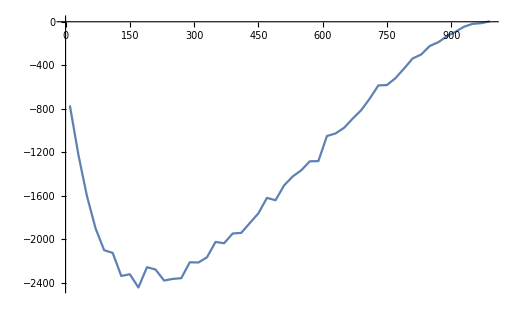

```mathematica
ListLinePlot[windowVsTotal,PlotRange->All]
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"imgs","histogram.png"}],histograms];
```

## 2-SMA Crossover Strategy

```mathematica
ma1 = Drop[MovingAverage[datedPrices[[All,2]],20],30];
ma2 = MovingAverage[datedPrices[[All,2]],50];
```

```mathematica
Take[ma1,10]
```

{14.4865,14.415,14.3345,14.249,14.1595,14.0665,14.0235,13.975,13.9265,13.8695}

```mathematica
Take[Drop[datedPrices[[All,2]],50-30],10]
```

{14.65,14.56,14.62,14.56,14.53,14.37,14.23,14.22,14.72,14.78}

```mathematica
Take[datedPrices[[All,2]],10]
```

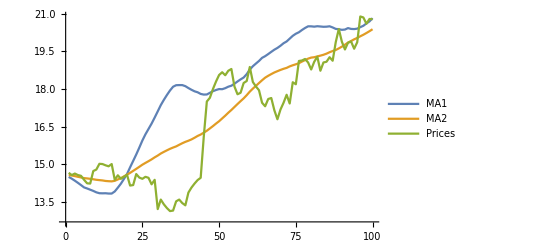

```mathematica
ListLinePlot[{Take[ma1,100],Take[ma2,100],Take[Drop[datedPrices[[All,2]],50-30],100]},PlotLegends->{"MA1","MA2","Prices"}]
```

```mathematica
First[ma1]<First[ma2]
```

```mathematica
RandomReal[1]<0.5
```

True

```mathematica
Centroid[matrix_]:={Total[matrix,{1}],Total[matrix,{2}]}.Range[Length[matrix]]/Total[matrix,-1];
ReversePoint[point_,max_]:={-1,1}*({0,max}-point);
```

```mathematica
DatedMovingAverage[datedPrices_,window_]:=Transpose[{Drop[datedPrices[[All,1]],window-1],MovingAverage[datedPrices[[All,2]],window]}];
SMA2Strategy[datedPrices_, window1_, window2_,transactionCost_]:=Block[{ma1,ma2,currentDatedPrices, lookingFor,buy={}, sell={}},
ma1 = Drop[MovingAverage[datedPrices[[All,2]],window1],window2-window1];
ma2 = MovingAverage[datedPrices[[All,2]],window2];
currentDatedPrices = Drop[datedPrices,window2-1];

lookingFor = If[First[ma1]<First[ma2],"BuySignal","SellSignal"];

Do[
If[lookingFor == "BuySignal" && ma1[[i]]>ma2[[i]],
AppendTo[buy,currentDatedPrices[[i]]];
lookingFor = "SellSignal";
];
If[lookingFor == "SellSignal" && ma1[[i]]<ma2[[i]],
AppendTo[sell,currentDatedPrices[[i]]];
lookingFor = "BuySignal";
];
,{i,1,Length[ma2]}
];

If[Length[buy]>Length[sell],AppendTo[sell,currentDatedPrices[[-1]]]];
If[Length[sell]>Length[buy],AppendTo[buy,currentDatedPrices[[-1]]]];

<|"BuyEvents"->buy,"SellEvents"->sell,"TotalEarnings"->(Total[(1-transactionCost)*sell[[All,2]]]-Total[(1+transactionCost)*buy[[All,2]]])|>
];
MakeEarningsMatrix[datedPrices_,from_,to_,window_ : 100]:=Block[{windows,earnings,matrix,centroidMatrix},
windows = Flatten[Table[{w1,w2},{w1,1,window},{w2,w1,window}],1];
earnings =Map[SMA2Strategy[Take[datedPrices,{from,to}], First[#],Last[#]]["TotalEarnings"]&,windows];
matrix = SparseArray[MapThread[#1->#2&,{windows,earnings}],{window,window}];
centroidMatrix = SparseArray[MapThread[If[#2>0,#1->#2,Nothing]&,{windows,earnings}],{window,window}];

MatrixPlot[matrix,
PlotLegends->Automatic,
Epilog->{PointSize[Large],Point[ReversePoint[Centroid[matrix],window]]}
]
];
SMA2StrategyPlot[datedPrices_,window1_,window2_]:=Block[{ma1,ma2, currentDatedPrices, strategyResults,plot},
ma1 = DatedMovingAverage[datedPrices,window1];
ma2 = DatedMovingAverage[datedPrices,window2];
strategyResults = SMA2Strategy[datedPrices, window1, window2];
If[strategyResults["BuyEvents"]=={} && strategyResults["SellEvents"]=={},
plot = DateListPlot[
{datedPrices,ma1,ma2},
Joined->{True,True,True},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->Placed[LineLegend[{"Price","MA "<>ToString[window1],"MA "<>ToString[window2]},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,{Thick,Blue},{Thick,Orange}},
PlotMarkers->{Automatic,None,None},
ImageSize->800,
PlotRange->All,
GridLines->Automatic,
PlotLabel->"Total earnings: "<>ToString[strategyResults["TotalEarnings"]]
];
Return[plot];
];
If[strategyResults["BuyEvents"]=={},
plot = DateListPlot[
{datedPrices,ma1,ma2,strategyResults["SellEvents"]},
Joined->{True,True,True,False},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->Placed[LineLegend[{"Price","MA "<>ToString[window1],"MA "<>ToString[window2],"Sell"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,{Thick,Blue},{Thick,Orange},Green},
PlotMarkers->{Automatic,None,None,Automatic},
ImageSize->800,
Filling->{4->{{2},Green}},
PlotRange->All,
GridLines->Automatic,
PlotLabel->"Total earnings: "<>ToString[strategyResults["TotalEarnings"]]
];
Return[plot];
];
If[strategyResults["SellEvents"]=={},
plot =DateListPlot[
{datedPrices,ma1,ma2,strategyResults["BuyEvents"]},
Joined->{True,True,True,False},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->Placed[LineLegend[{"Price","MA "<>ToString[window1],"MA "<>ToString[window2],"Buy"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,{Thick,Blue},{Thick,Orange},Red},
PlotMarkers->{Automatic,None,None,Automatic},
ImageSize->800,
Filling->{4->{{2},Red}},
PlotRange->All,
GridLines->Automatic,
PlotLabel->"Total earnings: "<>ToString[strategyResults["TotalEarnings"]]
];
Return[plot];
];


DateListPlot[
{datedPrices,ma1,ma2,strategyResults["BuyEvents"],strategyResults["SellEvents"]},
Joined->{True,True,True,False,False},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->Placed[LineLegend[{"Price","MA "<>ToString[window1],"MA "<>ToString[window2],"Buy","Sell"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,{Thick,Blue},{Thick,Orange},Red,Green},
PlotMarkers->{Automatic,None,None,Automatic,Automatic},
ImageSize->800,
Filling->{4->{{2},Red},5->{{2},Green}},
PlotRange->All,
GridLines->Automatic,
PlotLabel->"Total earnings: "<>ToString[strategyResults["TotalEarnings"]]
]
];
```

```mathematica
windows = Flatten[Table[{w1,w2},{w1,2,100,10},{w2,w1,100,10}],1];
```

```mathematica
earnings =ProgressMap[Table[SMA2Strategy[GeneratePrices[1000], First[#],Last[#],0.0]["TotalEarnings"],1000]&,windows];
```

```mathematica
earningsPerStock = Map[Total[#]/Length[earnings]&,earnings];
```

```mathematica
earningsByWindows = MapThread[Append[#1,#2]&,{windows,earningsPerStock}];
```

```mathematica
ListPlot3D[earningsByWindows]
```

-Graphics3D-